# Options

## Basic Exercises

### Question Subsection

Recall the separate function we wrote in the last exercise. For convenience, we have included the function definition here.

```mathematica
separate[a_Integer?Positive]:=Framed[a,Background->LightRed]
separate[a_Integer?Negative]:=Framed[a,Background->LightBlue]
separate[a_Real]:=Framed[a,Background->Yellow]
```

Define options for this function so that you can specify what color is used to highlight each class of numbers. The defaults should be the colors given in the function definition above.

#### Solution

```mathematica
Options[separate]={PositiveIntegerColor->LightRed,NegativeIntegerColor->LightBlue,RealColor->Yellow}
```

{PositiveIntegerColor→RGBColor[1, 0.85, 0.85],NegativeIntegerColor→RGBColor[0.87, 0.94, 1],RealColor→RGBColor[1, 1, 0]}

```mathematica
separate[a_Integer?Positive,OptionsPattern[]]:=Framed[a,Background->OptionValue[PositiveIntegerColor]]
separate[a_Integer?Negative,OptionsPattern[]]:=Framed[a,Background->OptionValue[NegativeIntegerColor]]
separate[a_Real,OptionsPattern[]]:=Framed[a,Background->OptionValue[RealColor]]
```

```mathematica
Options[separate]
```

{PositiveIntegerColor→RGBColor[1, 0.85, 0.85],NegativeIntegerColor→RGBColor[0.87, 0.94, 1],RealColor→RGBColor[1, 1, 0]}

```mathematica
separate[3]
```

3

```mathematica
separate[3,PositiveIntegerColor->LightGreen]
```

3

## Advanced Exercises

### Question Subsection

The Plot function takes two arguments. Rewrite it as myPlot so that it only takes the function to be plotted as an argument. The range of plotting should be passed to it as an option PlottingDomain->{x_min,x_max}. Note that the new function should be able to accept all the options of the original Plot function.

#### Hints

You will find the function FilterRules useful. 
If you evaluate Attributes[Plot], you will notice it has an attribute called HoldAll. We will get to this later. But for now, in order to make your function work, you will need to use Evaluate when you pass the options to the Plot function within myPlot.

#### Solution

```mathematica
Options[myPlot]=Join[Options[Plot],{PlottingDomain->{0,5}}];
```

```mathematica
myPlot[fun_,opts:OptionsPattern[]]:=(
xmin=OptionValue[PlottingDomain][[1]];
xmax=OptionValue[PlottingDomain][[2]];
ArrayPlot[fun[x],{x,xmin,xmax},Evaluate[FilterRules[{opts},Options[Plot]]]]
)
```

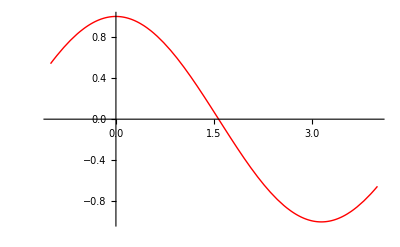

```mathematica
myPlot[Cos,PlottingDomain->{-1,4},PlotStyle->{Red,Thick}]
```